```mathematica
<<Neurogrid`
```

Notation::difform: The defined current default input format TraditionalForm`StandardForm differs from the current default output format TraditionalForm`TraditionalForm. The WorkingForm option will default to the current default output format, but the Notations, Symbolizations, and InfixNotations may behave differently than expected.

## ADC mismatch analysis

```mathematica
ImageResize[Import["/home/noza/work/Schematic Pictures/1V_ADC.png"],600]
```

-Graphics-

### Background

This section will analyze the 1V ADC design that is an adaptation of the New Gray Code ADC that is described on the wiki.  The goal of this analysis is to find I_Rout in terms of mismatch applied to I_Rin, and I_Sout in terms of mismatch applied to I_Sin.The operation of this ADC should be the same as the design on the wiki, except that it has been modified for 1V operation.  This means that the following equations describe the general operation of the ADC, where D_out is the digital bit that is output for the ADC stage in question, and I_Sout and I_Rout are the Signal and Reference currents, respectively, that are output to the next stage of the ADC.

D_out=I_Sin>I_Rin
I_Sout=2*Min(I_Sin,I_Rin)
I_Rout=Abs(I_Rin-I_Sin)

For the purposes of clarity, I have changed the naming convention from the wiki.  What used to be I_inV is now I_Sin, where the S stands for Signal.  In other words, this is trying to clarify that the signal that we are trying to digitize is I_Sin.  In order to digitize it is compared to I_Rin, where the R stands for Reference.  This signal is the same as I_inV on the wiki.  These naming conventions also apply to the output currents.

Transistors M_S_ and M_R_ comprise the portion of the ADC that determine I_Sout.  Likewise, transistors M_D_ calculate the absolute value of the Difference between I_Rin and I_Sin which gets sent on to the next stage as I_Rout.

Based on Ben's DAC Mismatch analysis and his characterization of transistor mismatch, we assume that the transistor threshold difference, normalized by U_T, can be assume to come from a log-normal distribution, defined by LogNormal[0, σ].

I assume that I_Sin and I_Rin are the reference currents from which mismatch will be compared.  This means that we don't need to include a mismatch term for I_Sin or I_Rin.

For this mismatch analysis, I have denoted the four branch currents, I_1, I_2, I_3, and I_4, individually.  This will hopefully make analyzing the mismatch easier, as each current will have a different mismatch constant taken from a distribution.  The mismatch constants will be written as as either s__ or r__ (depending on whether the mismatch is with relation to I_Sin or I_Rin, respectively, where _ is the unique identifier of the transistor that differs.   For instance, OverBar[I_Sin]=s_B2 I_Sin, where if s_B2 was equal to 1 (if M_B2 was exactly like M_B1), then OverBar[I_Sin]== I_Sin

To begin with, we know, based on circuit current analysis,  that:

OverBar[I_Sin]=s_B2 I_Sin
OverBar[I_Sin]=I_1+I_DS
I_Rin=I_4+I_DR
I_Sout=I_2+I_3
I_Rout=I_DS+I_DR
I_Rout≃|OverBar[I_Sin]-I_Rin|

Of these basic equations, the sixth (I_Rout) is the only one where the derivation/result is a little unintuitive.  As such, the analysis is written below:

I_Rout=OverBar[I_Sin]-I_1+I_Rin-I_4

Because of the nature of the upper portion of the circuit (the Min function calculator), we can assume that I_1≃I_4.  More importantly, the value of each of those currents will roughly equal Min(OverBar[I_Sin], I_Rin).  Therefore, I_Rout can equal either of the following equations, which is the same as the absolute value of the difference between I_Sin and I_Rin

I_Rout≃OverBar[I_Sin]-OverBar[I_Sin]+I_Rin-OverBar[I_Sin]=I_Rin-OverBar[I_Sin]
I_Rout≃OverBar[I_Sin]-I_Rin+I_Rin-I_Rin=OverBar[I_Sin]-I_Rin

### Mismatch in I_Sout

The first thing to note when analyzing the ADC circuit, is that there are 4 possible, high-level input situations depending on the following conditions:

I_Sin>>I_Rin	I_Sin is much greater than I_Rin
I_Sin≳I_Rin	I_Sin is only barely greater than I_Rin
I_Sin≲I_Rin	I_Sin is only barely smaller than I_Rin
I_Sin<<I_Rin	I_Sin is much smaller than I_Rin

In the first and last situations, the analysis is much easier than in the 2^nd or 3^rd situations.  This results from the fact that when the values of I_Sin≃I_Rin, then the mismatch can cause the circuit to activate I_S1 and I_R2 simultaneously.  This is a confounding factor because if there was no mismatch, then we could assume that if I_S1 is active, then so are I_S2,I_S3,and I_S4.  This would also apply to the I_R_ currents if they were active.

In the first case (I_Sin>>I_Rin), the following equations would apply:

I_1=r_R1/r_R4 I_Rin
I_2=r_R2/r_R4 I_Rin
I_3=r_R3/r_R4 I_Rin
I_4=I_Rin

I_Sout=(r_R2+r_R3)I_Rin/r_R4

In the last case (I_Sin<<I_Rin), the following equations would apply:

I_1=s_B2/s_B1 I_Sin
I_2=(s_S2 s_B2)/(s_S1 s_B1)I_Sin
I_3=(s_S3 s_B2)/(s_S1 s_B1)I_Sin
I_4=(s_S4 s_B2)/(s_S1 s_B1)I_Sin

I_Sout=(s_S2+s_S3)(s_B2 I_Sin)/(s_S1 s_B1)

In the 2^nd and 3^rd cases (I_Sin≳I_Rin, I_Sin≲I_Rin), the following equations would apply.  It should be noted that we are handling the 2^nd and 3^rd cases as the same situation because these situations are the same as saying when I_Sin≃I_Rin, where roughly equals is defined as within the mismatch’s effect to cause a transistor to turn on when it’s native value deems that it should turn off.

I_1=Min(r_R1/r_R4 I_Rin,s_B2/s_B1 I_Sin)
I_2=Min(r_R2/r_R4 I_Rin,(s_S2 s_B2)/(s_S1 s_B1)I_Sin)
I_3=Min(r_R3/r_R4 I_Rin,(s_S3 s_B2)/(s_S1 s_B1)I_Sin)
I_4=Min(I_Rin,(s_S4 s_B2)/(s_S1 s_B1)I_Sin)

I_Sout=Min(r_R2/r_R4 I_Rin,(s_S2 s_B2)/(s_S1 s_B1)I_Sin)+Min(r_R3/r_R4 I_Rin,(s_S3 s_B2)/(s_S1 s_B1)I_Sin)

It should be noted that this final result is actually the most general form of the mismatch of I_Sout because it also applies to the first two cases.  As such, moving forward, I will be using the 4 equations for each path’s current mismatch in my analysis.

### Revised mismatch in I_Sout

```mathematica
FullSimplify[Solve[{
Subscript[Ι, 1]==s1(Subscript[Ι, s1f]-Subscript[Ι, s1r]),
Subscript[Ι, 1]==r1(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 2]==s2(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]),
Subscript[Ι, 3]==s3(Subscript[Ι, s3f]),
Subscript[Ι, 3]==r3(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
Subscript[Ι, 4]==s4(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 4]==r4(Subscript[Ι, r4f]-Subscript[Ι, r4r]),

Subscript[Ι, s1f]==Subscript[Ι, s2f],
Subscript[Ι, r4f]==Subscript[Ι, r3f],

Subscript[Ι, s1r] Subscript[Ι, r2f]==Subscript[Ι, r1f] Subscript[Ι, s2r],
Subscript[Ι, s1r] Subscript[Ι, r3r]==Subscript[Ι, r1f] Subscript[Ι, s3f],
Subscript[Ι, s1r] Subscript[Ι, r4r]==Subscript[Ι, r1f] Subscript[Ι, s4f],
Subscript[Ι, s2r] Subscript[Ι, r3r]==Subscript[Ι, r2f] Subscript[Ι, s3f],
Subscript[Ι, s2r] Subscript[Ι, r4r]==Subscript[Ι, r2f] Subscript[Ι, s4f],
Subscript[Ι, r3r] Subscript[Ι, s4f]==Subscript[Ι, s3f] Subscript[Ι, r4r]
},{(*Subscript[Ι, Sout],*)Subscript[Ι, s1f],Subscript[Ι, s1r],Subscript[Ι, r1f],Subscript[Ι, r1r],Subscript[Ι, s2f],Subscript[Ι, s2r],Subscript[Ι, r2f],(*Subscript[Ι, r2r],*)Subscript[Ι, s3f],(*Subscript[Ι, s3r],*)Subscript[Ι, r3f],Subscript[Ι, r3r],Subscript[Ι, s4f],Subscript[Ι, s4r],Subscript[Ι, r4f],Subscript[Ι, r4r],Subscript[Ι, 2],Subscript[Ι, 3]}],Subscript[Ι, 1]>0&&Subscript[Ι, 2]>0&&Subscript[Ι, 3]>0&&Subscript[Ι, 4]>0&&s1>0&&r1>0&&s2>0&&r2>0&&s3>0&&r3>0&&s4>0&&r4>0]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→(s2 Ι_s1r (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1 Ι_s2r),Ι_r1r→(-(r2 Ι_1)/r1-s2 Ι_s1r+(s2 Ι_s1r (Ι_1+s1 Ι_s1r))/(s1 Ι_s2r))/r2,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_r2f→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1),Ι_r3f→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r),Ι_r3r→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)) Ι_s3f)/(r2 s1 Ι_s2r),Ι_s4f→(r4 (r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 Ι_4 Ι_s2r)/(r3 r4 s2 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_s4r→(r4 s4 (r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r3 Ι_4 (r4 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s4-r4 s2) Ι_s2r))/(r3 r4 s2 s4 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_r4f→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r),Ι_r4r→((r3 s2 (Ι_1+s1 Ι_s1r)+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 Ι_s2r)-Ι_4/r4,Ι_2→s2 (Ι_1/s1+Ι_s1r-Ι_s2r),Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_r2f→(s2 (Ι_1-s1 Ι_s2r))/(r2 s1),Ι_r3f→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f,Ι_r3r→(s2 (Ι_1-s1 Ι_s2r) Ι_s3f)/(r2 s1 Ι_s2r),Ι_s4f→(r4 (r3 s2 Ι_1+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 Ι_4 Ι_s2r)/(r3 r4 s2 (Ι_1-s1 Ι_s2r)),Ι_s4r→(r3 r4 s2 Ι_1 (s4 Ι_s3f-Ι_4)+s1 Ι_s2r (r3 (r4 s2-r2 s4) Ι_4+r4 (r2 s3-r3 s2) s4 Ι_s3f))/(r3 r4 s2 s4 (Ι_1-s1 Ι_s2r)),Ι_r4f→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f,Ι_r4r→(-s2/r2+(Ι_1 s2)/(r2 s1 Ι_s2r)+s3/r3) Ι_s3f-Ι_4/r4,Ι_2→(s2 Ι_1)/s1-s2 Ι_s2r,Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1r→Ι_r1f-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_s2r→0,Ι_r2f→(s2 Ι_1)/(r2 s1),Ι_s3f→0,Ι_r3f→Ι_r3r,Ι_s4f→0,Ι_s4r→-Ι_4/s4,Ι_r4f→Ι_r3r,Ι_r4r→Ι_r3r-Ι_4/r4,Ι_2→(s2 Ι_1)/s1,Ι_3→0},{Ι_s1f→0,Ι_s1r→-Ι_1/s1,Ι_r1r→Ι_r1f-Ι_1/r1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_r3f→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f,Ι_r3r→-(s1 Ι_r1f Ι_s3f)/Ι_1,Ι_s4f→(r3 Ι_1 Ι_4+r4 (r3 s1 Ι_r1f-s3 Ι_1) Ι_s3f)/(r3 r4 s1 Ι_r1f),Ι_s4r→Ι_4 (Ι_1/(r4 s1 Ι_r1f)-1/s4)+(1-(s3 Ι_1)/(r3 s1 Ι_r1f)) Ι_s3f,Ι_r4f→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f,Ι_r4r→(s3/r3-(s1 Ι_r1f)/Ι_1) Ι_s3f-Ι_4/r4,Ι_2→0,Ι_3→s3 Ι_s3f},{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_s2r→Ι_1/s1+Ι_s1r,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4},{Ι_s1f→Ι_1/s1+Ι_s1r,Ι_r1f→(s2 Ι_s1r (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1 Ι_s2r),Ι_r1r→(-(r2 Ι_1)/r1-s2 Ι_s1r+(s2 Ι_s1r (Ι_1+s1 Ι_s1r))/(s1 Ι_s2r))/r2,Ι_s2f→Ι_1/s1+Ι_s1r,Ι_r2f→(s2 (Ι_1+s1 (Ι_s1r-Ι_s2r)))/(r2 s1),Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 Ι_4 Ι_s2r)/(r4 s2 Ι_1+r4 s1 s2 Ι_s1r-r4 s1 s2 Ι_s2r),Ι_s4r→(Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2 (Ι_1+s1 Ι_s1r)))/(r4 s2 s4 (Ι_1+s1 (Ι_s1r-Ι_s2r))),Ι_r4f→0,Ι_r4r→-Ι_4/r4,Ι_2→s2 (Ι_1/s1+Ι_s1r-Ι_s2r),Ι_3→0},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_s2r→Ι_1/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4},{Ι_s1f→Ι_1/s1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→Ι_1/s1,Ι_r2f→(s2 (Ι_1-s1 Ι_s2r))/(r2 s1),Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 Ι_4 Ι_s2r)/(r4 s2 Ι_1-r4 s1 s2 Ι_s2r),Ι_s4r→-(Ι_4 (r4 s2 Ι_1+s1 (r2 s4-r4 s2) Ι_s2r))/(r4 s2 s4 (Ι_1-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4/r4,Ι_2→(s2 Ι_1)/s1-s2 Ι_s2r,Ι_3→0},{Ι_s1f→0,Ι_s1r→-Ι_1/s1,Ι_r1f→0,Ι_r1r→-Ι_1/r1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/(r4 s3),Ι_r3f→Ι_4/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4/s4,Ι_r4f→Ι_4/r4,Ι_r4r→0,Ι_2→0,Ι_3→(r3 Ι_4)/r4}}

```mathematica
FullSimplify[Solve[{
(*Subscript[Ι, 4]==r4(Subscript[Ι, r4f]-Subscript[Ι, r4r]),
Subscript[Ι, 4]==s4(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 3]==r3(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
(*Subscript[Ι, 3]==s3(Subscript[Ι, s3f]-Subscript[Ι, s3r]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]-Subscript[Ι, r2r]),*)
Subscript[Ι, 3]==s3(Subscript[Ι, s3f]),
Subscript[Ι, 2]==r2(Subscript[Ι, r2f]),
Subscript[Ι, 2]==s2(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 1]==r1(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 1]==s1(Subscript[Ι, s1f]-Subscript[Ι, s1r]),*)
Subscript[Ι, 1]==(Subscript[Ι, s1f]-Subscript[Ι, s1r]),
Subscript[Ι, 1]==(Subscript[Ι, r1f]-Subscript[Ι, r1r]),
Subscript[Ι, 2]==(Subscript[Ι, s2f]-Subscript[Ι, s2r]),
Subscript[Ι, 2]==(Subscript[Ι, r2f]),
(*Subscript[Ι, 2]==(Subscript[Ι, r2f]-Subscript[Ι, r2r]),
Subscript[Ι, 3]==(Subscript[Ι, s3f]-Subscript[Ι, s3r]),*)
Subscript[Ι, 3]==(Subscript[Ι, s3f]),
Subscript[Ι, 3]==(Subscript[Ι, r3f]-Subscript[Ι, r3r]),
Subscript[Ι, 4]==(Subscript[Ι, s4f]-Subscript[Ι, s4r]),
Subscript[Ι, 4]==(Subscript[Ι, r4f]-Subscript[Ι, r4r]),

(*Subscript[Ι, Sout]==Subscript[Ι, 2]+Subscript[Ι, 3],*)
Subscript[Ι, s1f]/s1==Subscript[Ι, s2f]/s2,
Subscript[Ι, r4f]/r4==Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s2r]/s2==Subscript[Ι, s1r]/s1 Subscript[Ι, r2f]/r2 Subscript[Ι, s2f]/s2,
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r3r]/r3==Subscript[Ι, r4r]/r4 Subscript[Ι, s3f]/s3 Subscript[Ι, r3f]/r3,*)
Subscript[Ι, s1r]/s1 Subscript[Ι, r2f]/r2==Subscript[Ι, r1f]/r1 Subscript[Ι, s2r]/s2,
Subscript[Ι, s1r]/s1 Subscript[Ι, r3r]/r3==Subscript[Ι, r1f]/r1 Subscript[Ι, s3f]/s3,
Subscript[Ι, s1r]/s1 Subscript[Ι, r4r]/r4==Subscript[Ι, r1f]/r1 Subscript[Ι, s4f]/s4,
Subscript[Ι, s2r]/s2 Subscript[Ι, r3r]/r3==Subscript[Ι, r2f]/r2 Subscript[Ι, s3f]/s3,
Subscript[Ι, s2r]/s2 Subscript[Ι, r4r]/r4==Subscript[Ι, r2f]/r2 Subscript[Ι, s4f]/s4,
Subscript[Ι, r3r]/r3 Subscript[Ι, s4f]/s4==Subscript[Ι, s3f]/s3 Subscript[Ι, r4r]/r4

(*Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s3r]/s3 Subscript[Ι, r3r]/r3==Subscript[Ι, s2r]/s2 Subscript[Ι, r2r]/r2 Subscript[Ι, s3f]/s3 Subscript[Ι, r3f]/r3,
Subscript[Ι, r3r]/r3 Subscript[Ι, s3r]/s3==Subscript[Ι, s3f]/s3 Subscript[Ι, r2r]/r2,
Subscript[Ι, s2r]/s2 Subscript[Ι, r2r]/r2==Subscript[Ι, r2f]/r2 Subscript[Ι, s3r]/s3,*)

(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1==Subscript[Ι, s1r]/s1 Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1==Subscript[Ι, s1r]/s1 Subscript[Ι, r4f]/r4,*)
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2==Subscript[Ι, s2r]/s2 Subscript[Ι, r3f]/r3,
(*Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2==Subscript[Ι, s2r]/s2 Subscript[Ι, r4f]/r4,*)
(*Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3==Subscript[Ι, r3r]/r3 Subscript[Ι, s1f]/s1,*)
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3==Subscript[Ι, r3r]/r3 Subscript[Ι, s2f]/s2,
(*Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4==Subscript[Ι, r4r]/r4 Subscript[Ι, s1f]/s1,*)
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4==Subscript[Ι, r4r]/r4 Subscript[Ι, s2f]/s2,
Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s3f]/s3==Subscript[Ι, s1r]/s1 Subscript[Ι, r3r]/r3 Subscript[Ι, s2f]/s2,
(*Subscript[Ι, s1f]/s1 Subscript[Ι, r1f]/r1 Subscript[Ι, s4f]/s4==Subscript[Ι, s1r]/s1 Subscript[Ι, r4r]/r4 Subscript[Ι, s2f]/s2,
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s3f]/s3==Subscript[Ι, s2r]/s2 Subscript[Ι, r3r]/r3 Subscript[Ι, s1f]/s1,
Subscript[Ι, s2f]/s2 Subscript[Ι, r2f]/r2 Subscript[Ι, s4f]/s4==Subscript[Ι, s2r]/s2 Subscript[Ι, r4r]/r4 Subscript[Ι, s1f]/s1,
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3 Subscript[Ι, r1f]/r1==Subscript[Ι, r3r]/r3 Subscript[Ι, s1r]/s1 Subscript[Ι, r4f]/r4,
Subscript[Ι, r3f]/r3 Subscript[Ι, s3f]/s3 Subscript[Ι, r2f]/r2==Subscript[Ι, r3r]/r3 Subscript[Ι, s2r]/s2 Subscript[Ι, r4f]/r4,
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r1f]/r1==Subscript[Ι, r4r]/r4 Subscript[Ι, s1r]/s1 Subscript[Ι, r3f]/r3,*)
Subscript[Ι, r4f]/r4 Subscript[Ι, s4f]/s4 Subscript[Ι, r2f]/r2==Subscript[Ι, r4r]/r4 Subscript[Ι, s2r]/s2 Subscript[Ι, r3f]/r3*)
},{Subscript[Ι, 2],Subscript[Ι, 3],(*Subscript[Ι, Sout],*)Subscript[Ι, s1f],Subscript[Ι, s1r],Subscript[Ι, r1f],Subscript[Ι, r1r],Subscript[Ι, s2f],Subscript[Ι, s2r],Subscript[Ι, r2f],(*Subscript[Ι, r2r],*)Subscript[Ι, s3f],(*Subscript[Ι, s3r],*)Subscript[Ι, r3f],Subscript[Ι, r3r],Subscript[Ι, s4f],Subscript[Ι, s4r],Subscript[Ι, r4f],Subscript[Ι, r4r]}],Subscript[Ι, 1]>0&&Subscript[Ι, 2]>0&&Subscript[Ι, 3]>0&&Subscript[Ι, 4]>0&&s1>0&&r1>0&&s2>0&&r2>0&&s3>0&&r3>0&&s4>0&&r4>0]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Ι_2→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_3→Ι_s3f,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→(r1 s2 Ι_s1r (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r))/(r2 s1^2 Ι_s2r),Ι_r1r→(r1 s2^2 Ι_s1r (Ι_1+Ι_s1r)-s1 (r2 s1 Ι_1+r1 s2 Ι_s1r) Ι_s2r)/(r2 s1^2 Ι_s2r),Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_r3f→((r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_r3r→(r3 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_s4f→(r4 s4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 s3 s4 Ι_4 Ι_s2r)/(r3 r4 s2 s3 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_s4r→(r3 s3 Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2^2 (Ι_1+Ι_s1r))+r4 s4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r3 r4 s2 s3 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_r4f→(r4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r),Ι_r4r→(r4 (r3 (Ι_1+Ι_s1r) s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r)-Ι_4},{Ι_2→(s2 Ι_1)/s1-Ι_s2r,Ι_3→Ι_s3f,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_r2f→(s2 Ι_1)/s1-Ι_s2r,Ι_r3f→((r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_r3r→(r3 s2 (s2 Ι_1-s1 Ι_s2r) Ι_s3f)/(r2 s1 s3 Ι_s2r),Ι_s4f→(s4 (r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f-r2 r3 s1 s3 Ι_4 Ι_s2r))/(r3 r4 s2 s3 (s2 Ι_1-s1 Ι_s2r)),Ι_s4r→(r3 r4 Ι_1 (s4 Ι_s3f-s3 Ι_4) s2^2+s1 Ι_s2r (r3 s3 (r4 s2-r2 s4) Ι_4+r4 (r2 s3-r3 s2) s4 Ι_s3f))/(r3 r4 s2 s3 (s2 Ι_1-s1 Ι_s2r)),Ι_r4f→(r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r),Ι_r4r→(r4 (r3 Ι_1 s2^2+s1 (r2 s3-r3 s2) Ι_s2r) Ι_s3f)/(r2 r3 s1 s3 Ι_s2r)-Ι_4},{Ι_2→(s2 Ι_1)/s1,Ι_3→0,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1r→Ι_r1f-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_s2r→0,Ι_r2f→(s2 Ι_1)/s1,Ι_s3f→0,Ι_r3f→Ι_r3r,Ι_s4f→0,Ι_s4r→-Ι_4,Ι_r4f→(r4 Ι_r3r)/r3,Ι_r4r→(r4 Ι_r3r)/r3-Ι_4},{Ι_2→0,Ι_3→Ι_s3f,Ι_s1f→0,Ι_s1r→-Ι_1,Ι_r1r→Ι_r1f-Ι_1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_r3f→(1-(r3 s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f,Ι_r3r→-(r3 s1 Ι_r1f Ι_s3f)/(r1 s3 Ι_1),Ι_s4f→(s4 (r3 r4 s1 Ι_r1f Ι_s3f+r1 s3 Ι_1 (r3 Ι_4-r4 Ι_s3f)))/(r3 r4 s1 s3 Ι_r1f),Ι_s4r→(r1 s3 s4 Ι_1 (r3 Ι_4-r4 Ι_s3f)+r3 r4 s1 Ι_r1f (s4 Ι_s3f-s3 Ι_4))/(r3 r4 s1 s3 Ι_r1f),Ι_r4f→r4 (1/r3-(s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f,Ι_r4r→r4 (1/r3-(s1 Ι_r1f)/(r1 s3 Ι_1)) Ι_s3f-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_s2r→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0},{Ι_2→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_3→0,Ι_s1f→Ι_1+Ι_s1r,Ι_r1f→(r1 s2 Ι_s1r (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r))/(r2 s1^2 Ι_s2r),Ι_r1r→(r1 s2^2 Ι_s1r (Ι_1+Ι_s1r)-s1 (r2 s1 Ι_1+r1 s2 Ι_s1r) Ι_s2r)/(r2 s1^2 Ι_s2r),Ι_s2f→(s2 (Ι_1+Ι_s1r))/s1,Ι_r2f→(s2 (Ι_1+Ι_s1r))/s1-Ι_s2r,Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 s4 Ι_4 Ι_s2r)/(r4 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_s4r→(Ι_4 (s1 (r4 s2-r2 s4) Ι_s2r-r4 s2^2 (Ι_1+Ι_s1r)))/(r4 s2 (s2 (Ι_1+Ι_s1r)-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_s2r→(s2 Ι_1)/s1,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0},{Ι_2→(s2 Ι_1)/s1-Ι_s2r,Ι_3→0,Ι_s1f→Ι_1,Ι_s1r→0,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→(s2 Ι_1)/s1,Ι_r2f→(s2 Ι_1)/s1-Ι_s2r,Ι_s3f→0,Ι_r3f→0,Ι_r3r→0,Ι_s4f→-(r2 s1 s4 Ι_4 Ι_s2r)/(r4 s2^2 Ι_1-r4 s1 s2 Ι_s2r),Ι_s4r→-(Ι_4 (r4 Ι_1 s2^2+s1 (r2 s4-r4 s2) Ι_s2r))/(r4 s2 (s2 Ι_1-s1 Ι_s2r)),Ι_r4f→0,Ι_r4r→-Ι_4},{Ι_2→0,Ι_3→(r3 Ι_4)/r4,Ι_s1f→0,Ι_s1r→-Ι_1,Ι_r1f→0,Ι_r1r→-Ι_1,Ι_s2f→0,Ι_s2r→0,Ι_r2f→0,Ι_s3f→(r3 Ι_4)/r4,Ι_r3f→(r3 Ι_4)/r4,Ι_r3r→0,Ι_s4r→Ι_s4f-Ι_4,Ι_r4f→Ι_4,Ι_r4r→0}}

### Mismatch in I_Rout

To analyze the mismatch in I_Rout, we start at the equation that most generally defines I_Rout.  From there, we use our I_Sout analysis to apply the mismatch that I_1 and I_4 would introduce to the circuit.

I_Rout=OverBar[I_Sin]-I_1+I_Rin-I_4
I_Rout=s_B2/s_B1 I_Sin-I_1+I_Rin-I_4

I_Rout=s_B2/s_B1 I_Sin-Min(r_R1/r_R4 I_Rin,s_B2/s_B1 I_Sin)+I_Rin-Min(I_Rin,(s_S4 s_B2)/(s_S1 s_B1)I_Sin)

### Function definitions for I_Sout and I_Rout

```mathematica
ISout[ISin_,IRin_,sB1_, sB2_,sS1_, rR2_,sS2_,rR3_,sS3_,rR4_]:=FullSimplify[Min[rR2/rR4 IRin, (sS2 sB2)/(sS1 sB1)ISin]+Min[rR3/rR4 IRin,(sS3 sB2)/(sS1 sB1)ISin],{IRin≥0,ISin≥0,sB1>0,sB2>0,sS1>0,rR2>0,sS2>0,rR3>0,sS3>0,rR4>0}]
IRout[ISin_,IRin_,sB1_,sB2_ ,rR1_,sS1_,rR4_,sS4_]:=FullSimplify[sB2/sB1 ISin-Min[rR1/rR4 IRin, sB2/sB1 ISin]+IRin-Min[IRin,(sS4 sB2)/(sS1 sB2) ISin],{IRin≥0,ISin≥0,sB1>0,sB2>0,rR1>0,sS1>0,rR4>0,sS4>0}]
```

```mathematica
"I_Sout"==ISout["I_Sin","I_Rin","s_B1","s_B2","s_S1","r_R2","s_S2","r_R3","s_S3","r_R4"]
"I_Rout"==IRout["I_Sin","I_Rin","s_B1","s_B2","r_R1","s_s1","r_R4","s_S4"]
```

I_Sout==min((I_Rin r_R2)/r_R4,(I_Sin s_B2 s_S2)/(s_B1 s_S1))+min((I_Rin r_R3)/r_R4,(I_Sin s_B2 s_S3)/(s_B1 s_S1))

I_Rout==-min((I_Rin r_R1)/r_R4,(I_Sin s_B2)/s_B1)-min(I_Rin,(I_Sin s_S4)/s_s1)+I_Rin+(I_Sin s_B2)/s_B1

### Function definitions for distributions

From Ben’s device analysis, we know that the mismatch parameter comes from a log-normal distribution.  The log-normal distribution comes from a normal distribution.  In other words, if X comes from a normal distribution (X∼𝒩(μ_n,σ_n^2)), then Y is defined as a log-normal distribution according to the following equation, Y=ⅇ^X.  The log-normal statistics (σ_l & μ_l) are related to normal’s  (σ_n & μ_n) according to the following two equations:

```mathematica
μLogNormal[μn_,σn_]=Mean[LogNormalDistribution[μn,σn]];
σLogNormal[μn_,σn_]=Simplify[Exp[Log[PowerExpand[StandardDeviation[LogNormalDistribution[μn,σn]]]]]];
Subscript[μ, l]-> μLogNormal[Subscript[μ, n],Subscript[σ, n]]
Subscript[σ, l]-> σLogNormal[Subscript[μ, n],Subscript[σ, n]]
```

μ_l→ⅇ^(μ_n+σ_n^2/2)

σ_l→√(ⅇ^(σ_n^2)-1) ⅇ^(μ_n+σ_n^2/2)

Assume we only have access to a log-normal distribution Y, defined as Y~ln𝒩(μ_n,σ_n^2), but we don’t know the underlying normal distribution’s statistics (μ_n, σ_n).  We can get the mean and standard deviation of the distribution (μ_l, σ_l) and then calculate/approximate the underlying normal’s mean and standard deviation based on the following two equations:

```mathematica
σNormal[μl_,σl_]=Refine[Reduce[σl^2==(σLogNormal[μn,σn]/.ⅇ^(μn+σn^2/2) -> μl)^2,σn],C[1]==0&&μl>0&&σl>0&&σn>0]⟦2,2⟧;
μNormal[μl_,σl_]=Refine[Reduce[μl==μLogNormal[μn,σNormal[μl,σl]]&&μl>0,μn],C[1]==0&&μl>0&&σl>0]⟦2⟧;
Subscript[μ, n]-> μNormal[Subscript[μ, l],Subscript[σ, l]]
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
```

μ_n→log(Root[#1^4 (μ_l^2+σ_l^2)-#1^2 μ_l^4&,4])

σ_n→√(log((μ_l^2+σ_l^2)/μ_l^2))

When σ_n^2≪1, these simplify to

```mathematica
μLogNormalApprox[μn_]=Simplify[PowerExpand[μLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
σLogNormalApprox[μn_,σn_]=Simplify[PowerExpand[σLogNormal[μn,σn]]/.(μn+σn^2/2)-> μn] ;
Subscript[μ, l]-> μLogNormalApprox[Subscript[μ, n]]
Subscript[σ, l]-> σLogNormalApprox[Subscript[μ, n],Subscript[σ, n]]
```

μ_l→ⅇ^μ_n

σ_l→ⅇ^μ_n √(ⅇ^(σ_n^2)-1)

Similarly, for σ_l^2≪1, the equation for μ_n simplifes as written below.  For σ_n, we don’t simplify it based on this assumption, because if we did σ_n would always equal 0, which is obviously incorrect.

```mathematica
μNormalApprox[μl_]=μn/.Refine[Solve[μl==μLogNormalApprox[μn],μn],C[1]==0]⟦1,1⟧;
Subscript[μ, n]-> μNormalApprox[Subscript[μ, l]]
Subscript[σ, n]-> σNormal[Subscript[μ, l],Subscript[σ, l]]
```

μ_n→log(μ_l)

σ_n→√(log((μ_l^2+σ_l^2)/μ_l^2))

### Plot of distribution of mismatch parameters

The following plot shows the log-normal distribution from which the mismatch terms are taken (in blue) and the normal distribution, 𝒩(μ_l,σ_l), that approximates this log-normal distribution (in orange).

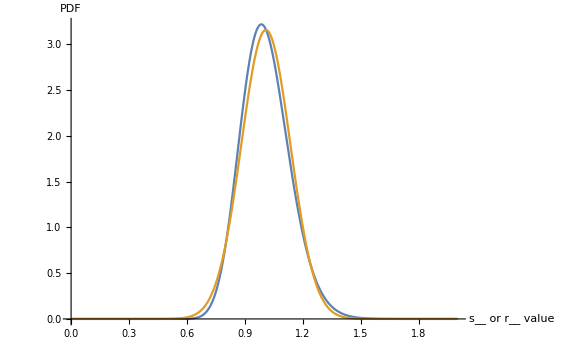

```mathematica
With[{μn=0, σn=0.125},
Plot[{
PDF[LogNormalDistribution[μn,σn],x],
PDF[NormalDistribution[μLogNormal[μn,σn],σLogNormal[μn,σn]],x]
},
{x,0,2},PlotRange->All,ImageSize->Large,AxesLabel->{"s__ or r__ value", "PDF"}]
]
```

```mathematica
PDFLNormDist[x_,μn_,σn_]:=PDF[LogNormalDistribution[μn,σn],x]
```

The following calculation shows that the probability of getting a negative number from the mismatch parameters is nearly 0, if we assume that the distribution is LogNormal[μ_n=0,σ_n=0.125].

```mathematica
PDFLNormDist[#,0,0.125]&/@{-0.01,-0.001,-0.0001,-0.00001,-0.000001,0,0.000001}
```

{0,0,0,0,0,0,8.43282181235552×10^-2647}

### Theoretical and numerical analysis of 1 ADC stage

```mathematica
Manipulate[
With[{μn=0,σn=0.125,numSamples=10^5,numBins=100},
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData=Select[RandomVariate[distISout,numSamples],#>0&];
distISoutEst=EstimatedDistribution[distISoutData,LogNormalDistribution[μs,σs]];
distISoutHist=HistogramDistribution[distISoutData,numBins];
(*
I'm throwing away data points that were selected that result in IRout to equal 0.  I do this because in practice, one of the two currents will always be somewhat larger than the other, therefore, there should always be some current going out Subscript[I, Rout]
*)
distIRoutData=Select[ RandomVariate[distIRout,numSamples],#>0&];
distIRoutEst=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
pISout=PDF[distISoutHist,x];
pIRout=PDF[distIRoutHist,x];
Grid[{{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}]
},(*{
Grid[{
{Style["I_Sout Estimated Distribution:"],distISoutEst},
{Style["I_Rout Estimated Distribution:"],distIRoutEst}
}]
},*){
Show[
DiscretePlot[{pISout,pIRout},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->Large,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst,x],PDF[distIRoutEst,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Large]
]
}}]
],
{{ISin,0.333333,"I_Sin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{IRin,0.666666,"I_Rin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{xMin,0,"x_min"},-0.5,0.5,0.1,Appearance->{"Labeled","Open"}},
{{xMax,1.0,"x_max"},0.5,5,0.1,Appearance->{"Labeled","Open"}}
]
```

### Theoretical and numerical analysis of 2 ADC stages

```mathematica
Manipulate[
With[{μn=0,σn=0.125/√2,numSamples=10^5,numBins=100,imgSz=500},
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData=Select[RandomVariate[distISout,numSamples],#>0&];
distISoutEst=EstimatedDistribution[distISoutData,LogNormalDistribution[μs,σs]];
distISoutHist=HistogramDistribution[distISoutData,numBins];
distIRoutData=Select[RandomVariate[distIRout,numSamples],#>0&];
distIRoutEst=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
pISout=PDF[distISoutHist,x];
pIRout=PDF[distIRoutHist,x];

distISout2= TransformedDistribution[ISout[ISin2,IRin2,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{ISin2\[Distributed]distISoutEst,IRin2\[Distributed]distIRoutEst,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout2= TransformedDistribution[IRout[ISin2,IRin2,sB1,sB2,rR1,sS1,rR4,sS4],{ISin2\[Distributed]distISoutEst,IRin2\[Distributed]distIRoutEst,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
distISoutData2= Select[Flatten[RandomVariate[distISout2,numSamples]],#>0&];
(*distISoutEst2= EstimatedDistribution[distISoutData2,LogNormalDistribution[μs,σs]];*)
distISoutEst2= EstimatedDistribution[distISoutData2,NormalDistribution[μs,σs]];
distISoutHist2=HistogramDistribution[distISoutData2,numBins];
distIRoutData2 = Select[Flatten[RandomVariate[distIRout2,numSamples]],#>0&];
distIRoutEst2 = EstimatedDistribution[distIRoutData2,NormalDistribution[μr,σr]];
distIRoutHist2=HistogramDistribution[distIRoutData2,numBins];
pISout2=PDF[distISoutHist2,x];
pIRout2=PDF[distIRoutHist2,x];

Grid[{
{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}],
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist2],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist2]},
{Style["μ_I_Rout:"],Mean[distIRoutHist2],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist2]}
}]
},{
Show[
DiscretePlot[{pISout,pIRout},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->imgSz,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst,x],PDF[distIRoutEst,x]},{x,xMin,xMax},PlotRange->All,ImageSize->imgSz]
],
Show[
DiscretePlot[{pISout2,pIRout2},{x,xMin,xMax,0.01},PlotRange->All,ImageSize->imgSz,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue"}],
(*Histogram[{distISoutData,distIRoutData},50,"PDF"],*)
Plot[{PDF[distISoutEst2,x],PDF[distIRoutEst2,x]},{x,xMin,xMax},PlotRange->All,ImageSize->imgSz]
]
}
}]
],
{{ISin,0.666666,"I_Sin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{IRin,0.333333,"I_Rin"},0,1,0.01,Appearance->{"Labeled","Open"}},
{{xMin,0,"x_min"},-0.5,0.5,0.1,Appearance->{"Labeled","Open"}},
{{xMax,1.5,"x_max"},0.5,5,0.1,Appearance->{"Labeled","Open"}}
]
```

### Theoretical and numerical analysis of B ADC stages

```mathematica
distIoutB[ISin0_,IRin0_,B_]:=
Module[{ISin=ISin0,IRin=IRin0,curDistIoutB},
With[{μn=0,σn=0.0125},
If[B>1,
curDistIoutB=distIoutB[ISin,IRin,B-1];
distISout= TransformedDistribution[ISout[ISinB,IRinB,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{ISinB\[Distributed]curDistIoutB⟦1⟧,IRinB\[Distributed]curDistIoutB⟦2⟧,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISinB,IRinB,sB1,sB2,rR1,sS1,rR4,sS4],{ISinB\[Distributed]curDistIoutB⟦1⟧,IRinB\[Distributed]curDistIoutB⟦2⟧,sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
,
distISout= TransformedDistribution[ISout[ISin,IRin,sB1,sB2,sS1,rR2,sS2,rR3,sS3,rR4],
{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR2\[Distributed]LogNormalDistribution[μn,σn],sS2\[Distributed]LogNormalDistribution[μn,σn],rR3\[Distributed]LogNormalDistribution[μn,σn],sS3\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn]}];
distIRout= TransformedDistribution[IRout[ISin,IRin,sB1,sB2,rR1,sS1,rR4,sS4],{sB1\[Distributed]LogNormalDistribution[μn,σn],sB2\[Distributed]LogNormalDistribution[μn,σn],rR1\[Distributed]LogNormalDistribution[μn,σn],sS1\[Distributed]LogNormalDistribution[μn,σn],rR4\[Distributed]LogNormalDistribution[μn,σn],sS4\[Distributed]LogNormalDistribution[μn,σn]}];
];
{distISout,distIRout}
]
]
```

```mathematica
SeedRandom[1234];
getIoutData[B0_,ISin0_,IRin0_]:=Module[{B=B0,ISin=ISin0,IRin=IRin0},
With[{numSamples=10^5,numBins=100},
(*With[{μn=0,σn=0.125,numSamples=10^5,numBins=100,ISin=0.666666,IRin=0.333333},*)
distIout= distIoutB[ISin,IRin,B];
distISout=distIout⟦1⟧;
distIRout=distIout⟦2⟧;

distISoutData=RandomVariate[distISout,numSamples];
distISoutHist=HistogramDistribution[distISoutData,numBins];
distISoutEstNorm=EstimatedDistribution[distISoutData,NormalDistribution[μs,σs]];
distISoutEstLN=EstimatedDistribution[Select[distISoutData,#>0&],LogNormalDistribution[μs,σs]];

distIRoutData=RandomVariate[distIRout,numSamples];
distIRoutHist=HistogramDistribution[distIRoutData,numBins];
distIRoutEstNorm=EstimatedDistribution[distIRoutData,NormalDistribution[μr,σr]];
distIRoutEstLN=EstimatedDistribution[Select[distIRoutData,#>0&],LogNormalDistribution[μr,σr]];
];
{distISoutHist,distIRoutHist,distISoutEstNorm,distIRoutEstNorm,distISoutData,distIRoutData, distISoutEstLN, distIRoutEstLN}
]
```

```mathematica
With[{numB=4},
ISin0=0.5-1/2^numB;
IRin0=0.5+1/2^numB;
IOutTable=Table[getIoutData[b,ISin0,IRin0],{b,1,numB}];
]
```

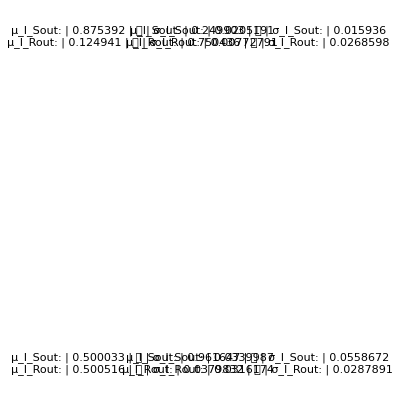
{I_Sin:,0.4375,	,I_Rin:,0.5625}
-Graphics-

```mathematica
With[{numB=4,xMin=0.0,xMax=1.5},
distPlots=Reap[
(
distISoutHist=IOutTable⟦#⟧⟦1⟧;
distIRoutHist=IOutTable⟦#⟧⟦2⟧;
distISoutEstNorm=IOutTable⟦#⟧⟦3⟧;
distIRoutEstNorm=IOutTable⟦#⟧⟦4⟧;
distISoutData=IOutTable⟦#⟧⟦5⟧;
distIRoutData=IOutTable⟦#⟧⟦6⟧;
distISoutEstLN=IOutTable⟦#⟧⟦7⟧;
distIRoutEstLN=IOutTable⟦#⟧⟦8⟧;

p1=DiscretePlot[{PDF[distISoutHist,x],PDF[distIRoutHist,x]},{x,xMin,xMax,0.01},ImageSize->Full,PlotLegends->Placed[{"I_Sout","I_Rout"},{Right,Top}],AxesLabel->{"I_outValue","PDF"}, PlotRange->All];
p2=Plot[{PDF[distISoutEstNorm,x],PDF[distIRoutEstNorm,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Full];
p3=Histogram[{distIRoutData,distIRoutData},50,"PDF"];
p4=Plot[{PDF[distISoutEstLN,x],PDF[distIRoutEstLN,x]},{x,xMin,xMax},PlotRange->All,ImageSize->Full,PlotStyle->{Dashed,Dashed}];
Sow[
Grid[{
{
Grid[{
{Style["μ_I_Sout:"],Mean[distISoutHist],"\t",Style["σ_I_Sout:"],StandardDeviation[distISoutHist]},
{Style["μ_I_Rout:"],Mean[distIRoutHist],"\t",Style["σ_I_Rout:"],StandardDeviation[distIRoutHist]}
}]
},{
Show[{p1(*,p2,p4*)}]
}
}]]
)&/@Range[1,numB]];
Grid[{
{{Style["I_Sin:"],ISin0,"\t",Style["I_Rin:"],IRin0}},
{GraphicsGrid[ArrayReshape[distPlots⟦2⟧, {2, 2}], ImageSize->Full]}
}]
]
```

TransformedDistribution[a+b X,X\[Distributed]LogNormalDistribution[mu,sigma]]

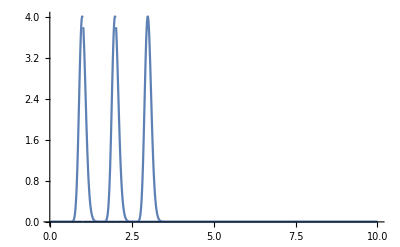

```mathematica
TransformedDistribution[b X+a, X\[Distributed]LogNormalDistribution[mu, sigma]]
Plot[Table[PDF[%,X]/.{a-> valA, b-> 1, mu-> 0, sigma-> 0.1}, {valA, 0, 2, 1}], {X, 0, 10}, PlotRange->All]
```

LogNormalDistribution[log(b)+mu,sigma]

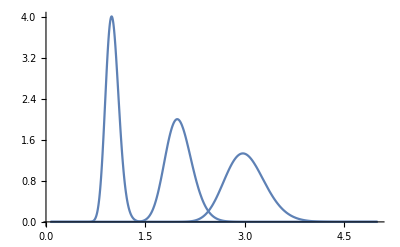

```mathematica
TransformedDistribution[b X, X\[Distributed]LogNormalDistribution[mu, sigma]]
Plot[Table[PDF[%,X]/.{b-> valB, mu-> 0, sigma-> 0.1}, {valB, 1, 3, 1}], {X, 0, 5}, PlotRange->All]
```